```mathematica
SZ1[R_,NN_,Ra_,k_]:=NN/Ra*(R/Ra)^(k-1)*k^k*Exp[-k*R/Ra]/(Gamma[k])
```

```mathematica
Integrate[SZ1[R,1,Ra,k]*R/Ra,{R,0,Infinity},Assumptions -> k>0 && Ra>0]
```

1

```mathematica
SZ2[R_,NN_,Ra_,k_]:=NN*(k/Ra)^(k+1)*R^k*Exp[-k*R/Ra]/Gamma[k+1]
```

```mathematica
Integrate[SZ2[R,1,Ra,k],{R,0,Infinity},Assumptions -> k>0 && Ra>0]
```

1

```mathematica
FullSimplify[SZ1[R,1,Ra,k]]
```

(ⅇ^(-(k R)/Ra) k^k (R/Ra)^k)/(R Gamma[k])

```mathematica
FullSimplify[SZ1[R,1,Ra,k]*R/Ra]
```

(ⅇ^(-(k R)/Ra) k^k (R/Ra)^k)/(Ra Gamma[k])

```mathematica
SZ2[R,N,Ra,k]
```

(ⅇ^(-(k R)/Ra) N R^k (k/Ra)^(1+k))/Gamma[1+k]

```mathematica
xmode1:=Assuming[k>0 && Ra>0,Solve[D[SZ1[R,1,Ra,k],R]==0,R]]
```

```mathematica
xmode1
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→0^(1/k) Ra},{R→(-Ra+k Ra)/k}}

```mathematica
SZ1[R*k/(k-1),1,Ra,k]
```

(ⅇ^(-(k^2 R)/((-1+k) Ra)) k^(-1+k) ((k R)/((-1+k) Ra))^(-1+k))/(Ra Gamma[-1+k])

```mathematica
xmode2:=Solve[D[SZ2[R,1,Ra,k],R]==0,R]
```

```mathematica
xmode2
```

{{R→Ra}}

```mathematica
Nth1:=Integrate[SZ1[R(k-1)/k,1,Ra,k]*R^n,{R,0,Infinity},Assumptions -> k>1 && Ra>0&&n>0]
```

```mathematica
FullSimplify[Nth1]
```

((-1+k)^(-1-n) k Ra^n Gamma[k+n])/Gamma[k]

```mathematica
Nth2:=Integrate[SZ2[R,1,Ra,k]*R^n,{R,0,Infinity},Assumptions -> k>0 && Ra>0&&n>0]
```

```mathematica
FullSimplify[Nth2]
```

((Ra/k)^n Gamma[1+k+n])/Gamma[1+k]

```mathematica
variance2:=Simplify[Integrate[SZ2[R,1,Ra,k]*R^2,{R,0,Infinity},Assumptions -> k>0 && Ra>0] -(Integrate[SZ2[R,1,Ra,k]*R,{R,0,Infinity},Assumptions -> k>0 && Ra>0] )^2]
```

```mathematica
variance2
```

((1+k) Ra^2)/k^2

```mathematica
Integrate[SZ1[R,1,Ra,k]*R,{R,0,Infinity},Assumptions -> k>0 && Ra>0]
```

Ra

```mathematica
variance1:=Simplify[Integrate[SZ1[R,1,Ra,k]*R^2,{R,0,Infinity},Assumptions -> k>0 && Ra>0] -(Integrate[SZ1[R,1,Ra,k]*R,{R,0,Infinity},Assumptions -> k>0 && Ra>0] )^2]
```

```mathematica
variance1
```

Ra^2/k

```mathematica
Simplify[Integrate[SZ1[R,1,Ra,k]*(R-Ra)^2,{R,0,Infinity},Assumptions -> k>0 && Ra>0] ]
```

Ra^2/k

```mathematica
FullSimplify[SZ1[R,1,Ra,k]*R/Ra]-SZ2[R,1,Ra,k]
```

(ⅇ^(-(k R)/Ra) k^k (R/Ra)^k)/(Ra Gamma[k])-(ⅇ^(-(k R)/Ra) R^k (k/Ra)^(1+k))/Gamma[1+k]

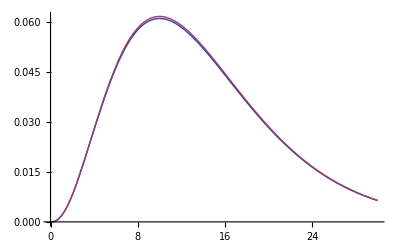

```mathematica
Plot[{SZ1[R,1,10,2.5]*R/10,1.01*SZ2[R,1,10,2.5]},{R,0,30}]
```